```mathematica
Determining Se and Sm from the skyrmion field
```

```mathematica
R  = 1;
θ[r]:= π(1-Exp[-r^2/R^2]); (*Azimuthal angle*)
Integrate[2π r (Cos[θ[r]]+1),{r,0,Infinity}]
SeCoefficient=%//N
Sm = Integrate[2π r^2 Sin[θ[r]],{r,0,Infinity}]
SmCoefficient=%//N
```

π (EulerGamma-CosIntegral[π]+Log[π])

5.17822

∫_0^∞ 2 π r^2 Sin[(1-ⅇ^(-r^2)) π]ⅆr

6.53068

{-1.44897,-1.44897,1.44897,1.44897}

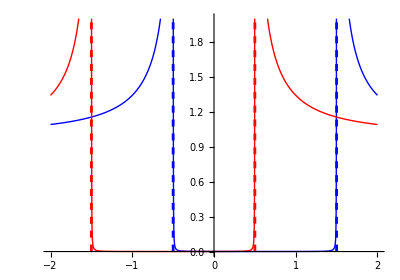

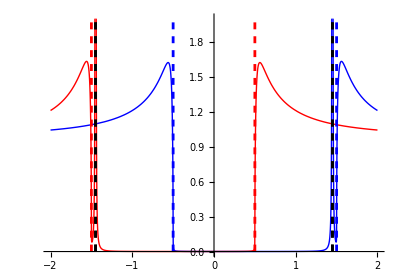

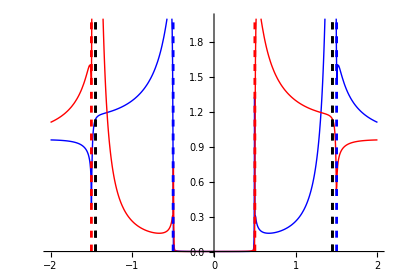

```mathematica
Plotting  LDOS near the skyrmion ;
id =({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});σx=({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}}) ; σy=({{0, -ⅈ, 0, 0}, {ⅈ, 0, 0, 0}, {0, 0, 0, -ⅈ}, {0, 0, ⅈ, 0}}); σz =({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}}); τx = ({{0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}, {0, 1, 0, 0}}); τz =({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
EF = 1; p =1; ρ= 1/(4π);  (*Fermi energy and momentum fix DOS*)
Δ = 0.25 EF;S = 0.5Δ;  (*Gap and external magnetization*)
R =1;  Se = R^2 S SeCoefficient; Sm = R^3 S SmCoefficient;(*Parameters of skyrmion: size and effective out-of-plane spin, effective in-plane monopole moment*)

 X =Se π ρ;  ES =  (1-X^2)/(1+X^2);  (*position of conventional YSR state*)
Γ= 0.0001; (*imaginary infinitesimal*)
ClearAll["ω","LDOS","G","barG"]

G[ω_]:=-π ρ ((id+σz)/2) .(((ω+ⅈ Γ-S)id +Δ τx)/(√(Δ^2-(ω+ⅈ Γ-S)^2)))-π ρ ((id-σz)/2) .(((ω+ⅈ Γ+S)id +Δ τx)/(√(Δ^2-(ω+ⅈ Γ+S)^2)));
barG[ω_]:= -π ρ ((id-σz)/2) .(((ω+ⅈ Γ-S)id +Δ τx)/(√(Δ^2-(ω+ⅈ Γ-S)^2)))-π ρ ((id+σz)/2) .(((ω+ⅈ Γ+S)id +Δ τx)/(√(Δ^2-(ω+ⅈ Γ+S)^2)));
T[ω_]:=Inverse[id+Se σz.G[ω]-Sm^2 p^2 G[ω].barG[ω]].(-Se σz+Sm^2 p^2 barG[ω]);
T0[ω_]:=Inverse[id+Se σz.G[ω]].(-Se σz);

LDOSσ[ω_,σ_]:= -1/π Im[Tr[((id+τz)/2).((id+σ)/2).(G[ω]+G[ω].T[ω].G[ω])]];
LDOSσ0[ω_,σ_]:= -1/π Im[Tr[((id+τz)/2).((id+σ)/2).(G[ω]+G[ω].T0[ω].G[ω])]];
LDOSσAwayFromSkyrmion[ω_,σ_]:= -1/π Im[Tr[((id+τz)/2).((id+σ)/2).G[ω]]];


Solution for the  T-matrix poles;


ClearAll["ω","g","barg"]
g=-π ρ ((id+σz)/2) .(((ω-S)id +Δ τx)/(√(Δ^2-(ω-S)^2)))-π ρ ((id-σz)/2) .(((ω+S)id +Δ τx)/(√(Δ^2-(ω+S)^2)));
barg  = -π ρ ((id-σz)/2) .(((ω-S)id +Δ τx)/(√(Δ^2-(ω-S)^2)))-π ρ ((id+σz)/2) .(((ω+S)id +Δ τx)/(√(Δ^2-(ω+S)^2)));
(*Find determinant and find roots*)
ListOfTmatrixPoles=(ω/.Solve[ Simplify[Det[id+Se σz.g]]==0,ω])/Δ//Re 

Preparation before plotting ;

maxY = 2; (* PlotRange/.AbsoluteOptions[gr1,PlotRange] //Flatten//Last;*)
VerticalLine [ω_,color_] :=Line[{{ω,-0.1},{ω,maxY +0.1}}]; (*define auxiliarly function*)
aspRatio = 0.7;




Plot LDOS for pure ferromagnet ;
gr1 = Plot[{LDOSσAwayFromSkyrmion[Δ ω,σz]/ρ,LDOSσAwayFromSkyrmion[Δ ω,-σz]/ρ},{ω,-2,2},PlotStyle->{{Thick,Blue},{Thick, Red}},
TicksStyle-> Directive[18],AspectRatio->0.7,PlotRange->{{-2,2},{0,maxY}}];
gr1a = Graphics[{Blue,Dashed,Thickness[0.005],VerticalLine /@ {1+S/Δ,-1+S/Δ},Red,VerticalLine /@ {1-S/Δ,-1-S/Δ}}];
Show[gr1,gr1a]

Plot LDOS for skyrmion with simple T-matrix     ;
gr2 = Plot[{LDOSσ0[Δ ω,σz]/ρ,LDOSσ0[Δ ω,-σz]/ρ},{ω,-2,2},PlotStyle->{{Thick,Blue},{Thick, Red},{Thick,Blue,Thickness[0.005],Dashing[0.05]},{Thick, Red,Thickness[0.005],Dashing[0.05]},{Thick, Black},{Thickness[0.01],Dashing[0.05],Green//Darker}},
TicksStyle-> Directive[18],AspectRatio->aspRatio,PlotRange->{{-2,2},{0,maxY}},MaxRecursion->6];
gr2a = Graphics[{Blue,Dashed,Thickness[0.005],VerticalLine /@ {1+S/Δ,-1+S/Δ},Red,VerticalLine /@ {1-S/Δ,-1-S/Δ},Black,VerticalLine/@ ListOfTmatrixPoles}];
Show[gr2,gr2a]

Plot LDOS for skyrmion with modified T-matrix     ;

gr3 = Plot[{LDOSσ[Δ ω,σz]/ρ,LDOSσ[Δ ω,-σz]/ρ},{ω,-2,2},PlotStyle->{{Thick,Blue},{Thick, Red},{Thick, Black},{Thickness[0.01],Dashing[0.05],Green//Darker}},
TicksStyle-> Directive[18],AspectRatio->aspRatio,PlotRange->{{-2,2},{0,maxY}},MaxRecursion->4];

Show[gr3,gr2a]
```

```mathematica
u
```

```mathematica
N[1/(2π)]
```

```mathematica
E
```

```mathematica
Integrate[Sin[x]/x,{x,0,Infinity}]
Integrate[Sin[x]/x Sin[x/3]/(x/3),{x,0,Infinity}]
Integrate[Sin[x]/x Sin[x/3]/(x/3)Sin[x/5]/(x/5),{x,0,Infinity}]
Integrate[Sin[x]/x Sin[x/3]/(x/3)Sin[x/5]/(x/5)Sin[x/6]/(x/6),{x,0,Infinity}]

Integrate[Sin[x]/x Sin[x/3]/(x/3)Sin[x/5]/(x/5)Sin[x/7]/(x/7)Sin[x/9]/(x/9)Sin[x/11]/(x/11)Sin[x/13]/(x/13)Sin[x/15]/(x/15),{x,0,Infinity}]
```

π/2

π/2

π/2

«1 more identical outputs»

(467807924713440738696537864469 π)/935615849440640907310521750000

```mathematica
1/3+1/5+1/7+1/9+1/11+1/13+1/15
```

46027/45045